```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/00_SplinePack-034.nb"]  // Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"] //Quiet;

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/TP_ImProc_01-m101.wl"] //Quiet;



Clear[SavitzkyGolayFilterExtended]


SavitzkyGolayFilterExtended[DOrder_,M_,nl_,nr_,data_] := Module[{i,j,p,t},
p = Table[t^i,{i,0,M}];
j = nl+nr+1;
i = Range[j];
Join[
D[Fit[Transpose[{i,Take[data,   j]}],p,t],{t,DOrder}]/.t->Take[i,  nl],
SavitzkyGolayFilter[DOrder,M,nl,nr,data],
D[Fit[Transpose[{i,Take[data,-j]}],p,t],{t,DOrder}]/.t->Take[i,-nr]]];



Clear[
ParamPadToTake,
ParamTakeToPad]


ParamPadToTake[ImgDim_,LeftRightBottomTop_] := {
{LeftRightBottomTop[[2,2]]+1,If[ListQ[ImgDim],ImgDim[[2]],-1]-LeftRightBottomTop[[2,1]]},
{LeftRightBottomTop[[1,1]]+1,If[ListQ[ImgDim],ImgDim[[1]],-1]-LeftRightBottomTop[[1,2]]}};


ParamTakeToPad[ImgDim_,RowsCols_] := Module[{LeftRightBottomTop},
LeftRightBottomTop = Reverse[RowsCols];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[1]] -= 1;
LeftRightBottomTop[[2]] = ImgDim-LeftRightBottomTop[[2]];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[2]] = Reverse[LeftRightBottomTop[[2]]];
LeftRightBottomTop];



Clear[
LoadFromTIF,
SaveAsTIF]


LoadFromTIF[CheckBitLength_,fname_] := Module[{X},
X = Import[fname];
X[[-1]] = ReadQRCode[X[[-1]]];
If[
If[TrueQ[CheckBitLength],
SameQ[
Piecewise[{{1,#≤1},{8,1<#≤8}},16]&/@Ceiling[Log[2,X[[-1,1]]]],
Ceiling[Log[2,Map[Length[Union@@ImageData[#]]&,Drop[X,-1]]]]],
True],
X[[-1]] = X[[-1,2]];
Fold[
ReplacePart[#1,#2[[1]],#2[[2]]]&,
X[[-1]],
Transpose[
{Drop[X,-1],
Position[X[[-1]],Image]}]]]];


SaveAsTIF[fname_,data_] := Module[{x,X},
X = data/.x_:>MyVectorPlaceholder/;ImageQ[x];
X = Append[
Extract[data,Position[X,MyVectorPlaceholder]],
X/.MyVectorPlaceholder->Image];
X[[-1]] = {Map[Length[Union@@ImageData[#]]&,Drop[X,-1]],X[[-1]]};
X[[-1]] = WriteQRCode[X[[-1]]];
MDExport[fname,X,"ImageEncoding"->"LZW"]];



Clear[ChangeImgDims]


ChangeImgDims[
  B_?ImageQ,
nx_?IntegerQ,
ny_?IntegerQ,
padding_] := Module[{R,x,y},
{x,y} = {nx,ny}-ImageDimensions[R=B];
If[y<0,
y = {Quotient[-y,2],-y};
y = {First[y],Subtract@@y}+{1,-1};
R = ImageTake[R,y],
If[y>0,
y = {y,Quotient[y,2]};
y = {Last[y],Subtract@@y};
R = ImagePad[R,{{0,0},y},padding]]];
If[x<0,
x = {Quotient[-x,2],-x};
x = {First[x],Subtract@@x}+{1,-1};
R = ImageTake[R,All,x],
If[x>0,
x = {x,Quotient[x,2]};
x = {Last[x],Subtract@@x};
R = ImagePad[R,{x,{0,0}},padding]]];
R];
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

```mathematica
$HistoryLength = 10;
```

```mathematica
PrependTo[MyTS,FontSize->24];
```

```mathematica
Clear[
CountMarker,
CountMaximum]

CountMaximum = 0;

CountMarker := Module[{o,s,x,y},
{x,y,s,o} = #;
s = N[Sqrt[s]];
s = y+{-Min[s,y],s};
If[o,CountMaximum = Max[CountMaximum,s[[2]]]];
{If[o,Blue,Green],
Point[{x,y}],
Line[
{{x,s[[1]]},
{x,s[[2]]}}]}]&;
```

```mathematica
Clear[CredibilityRange]

CredibilityRange := Module[{m,p},
m = Flatten[#];
p = Select[m,(Head[#]===Line  )&];
m = Select[m,(Head[#]===Point)&];
m = Append[
Transpose[First/@p],
                       First/@m];
m = Map[SortBy[#,First]&,m];
m[[2]] = Reverse[m[[2]]];
{Polygon[Join@@Most[m]],
Line[Last[m]]}]&;
```

```mathematica
Clear[ToEnglish]
ToEnglish = First[Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/EmissionRatePlotData.dat"]]
```

{Kl→C,Kl02→C2,Tr→T,Tr01→T1,Ob→O,Ob02→O2,Ob03→O3,Ob04→O4,Ob05→O5,Ob06→O6,Ob07→O7,Ob08→O8,Ob09→O9,Ob10→O10,Ob11→O11,Ob12→O12,Qu→F,Qu01→F1,Qu02→F2,Qu03→F3,Qu04→F4,Qu05→F5,Qu06→F6,Qu07→F7,Qu09→F9,Qu10→F10,Qu11→F11,Qu12→F12,Qu13→F13,Qu14→F14,Qu15→F15,Qu16→F16,Qu17→F17,Qu18→F18,Qu19→F19,Qu20→F20,KP→S,KP01→S1,KP02→S2,KP03→S3,KP04→S4,KP05→S5,KP06→S6,KP07→S7,KP08→S8,KP09→S9,KP10→S10,KP11→S11,KP12→S12,Atmen→Breathing,Aufgabe→Task,Beginn (s)→Begin (s),Emissionsrate (P/s)→Emission rate (P/s),Ende (s)→End (s),Musikspiel→Playing,Musikspiel mit Schutz→Playing With Surgical Mask,Partikel/Wasser (P/mg)→Particles/Water (P/mg),Sprechen→Speaking,Sprechen mit MNS→Speaking With Surgical Mask,Wasseremission (mg/s)→Water emission (mg/s)}

```mathematica
DatenOrdner = NotebookDirectory[]~~"output directory\\"
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\

```mathematica
Clear[x,X,Y,Z]
 Z=Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20220301-01/EmissionRates.dat"];
Length[Z]
```

1804

```mathematica
Clear[Y]
Y = {"Proband","Instrument","Player","Task","Bins","EmissionRateSignificanceLevel","EmissionRateµσCI","EmissionRateDistribution"}/.Z;
Y = Select[Y,UnsameQ[#[[8]],"EmissionRateDistribution"]&];
Y = Select[Y,(#[[7,4]]>=0.01)&];
Y = Select[Y,(#[[6]]>=0.001)&];
Y = Map[ReplacePart[#,DeleteDuplicates[Last/@#[[5]]],5]&,Y];
Y = Select[Y,(Length[#[[5]]]==1)&];
Y = Transpose[Y];
Y[[5]] = First/@Y[[5]];
Y[[5]] = Y[[5]]/."Aerosol"->N[-1];
Y[[1]] = Y[[1]]/.ToEnglish;
Y[[4]] = Y[[4]]/.ToEnglish;
Union[Y[[4]]]
Y[[7]] = LessEqual@@@Map[Insert[Clip[Drop[#,2],{0,Infinity}],x,2]&,Y[[7]]];
Y[[7]] = Function/@(Y[[7]]/.x->#);
Y = Join[Take[Y,5],Y[[{8,7}]]];
Y = Transpose[Y];
Y = Select[Y,UnsameQ[#[[5]],"Droplets"]&];
Y = Select[Y,(#[[5]]<=5)&];                                              (*    Aerosol    *)
Union[Map[#[[5]]&,Y]]
```

{Breathing,Playing,Playing With Surgical Mask,Speaking,Speaking With Surgical Mask}

{-1.,0.251496,0.40694,0.8,1.57226,2.99099}

```mathematica
(*hier wird die Kontrollgruppe ausgeschlossen*)

Y = Select[Y,UnsameQ[#[[2]],"KP"]&];
```

```mathematica
Length[Y]
```

669

Speaking

4.44089×10^-16

{0.251496,0.40694,0.8,1.57226,2.99099}

2594

17

{{Qu,12},{Ob,4},{Kl,1}}

{{F1,F4,F5,F6,F7,F10,F13,F15,F17,F18,F19,F20},{O4,O6,O9,O12},{C}}

{Flute,Oboe,Clarinet}

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

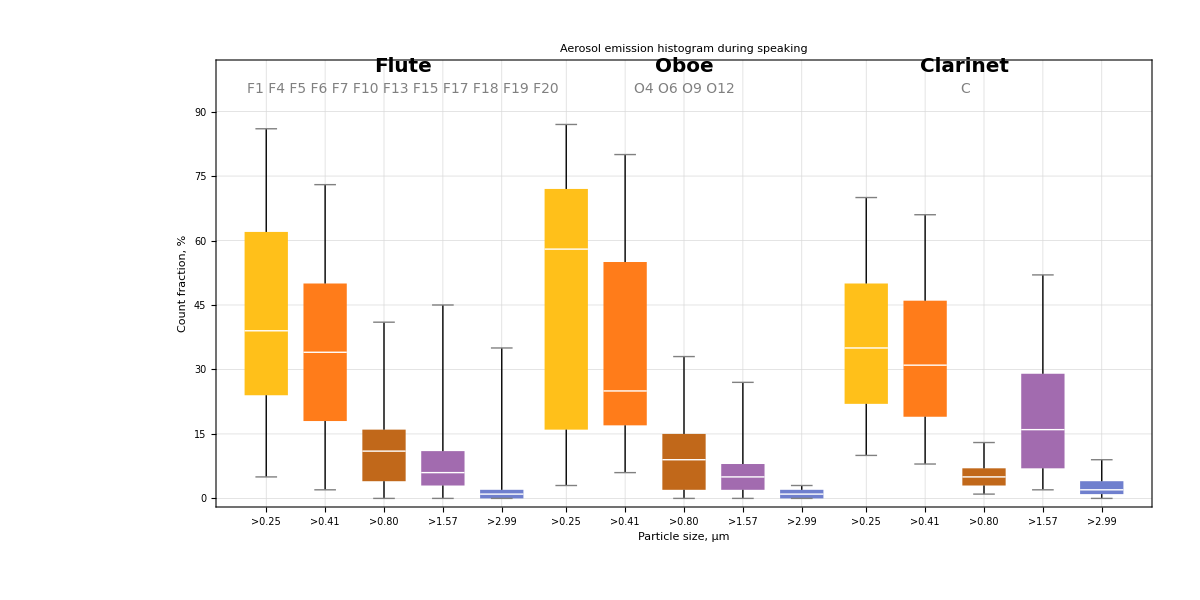

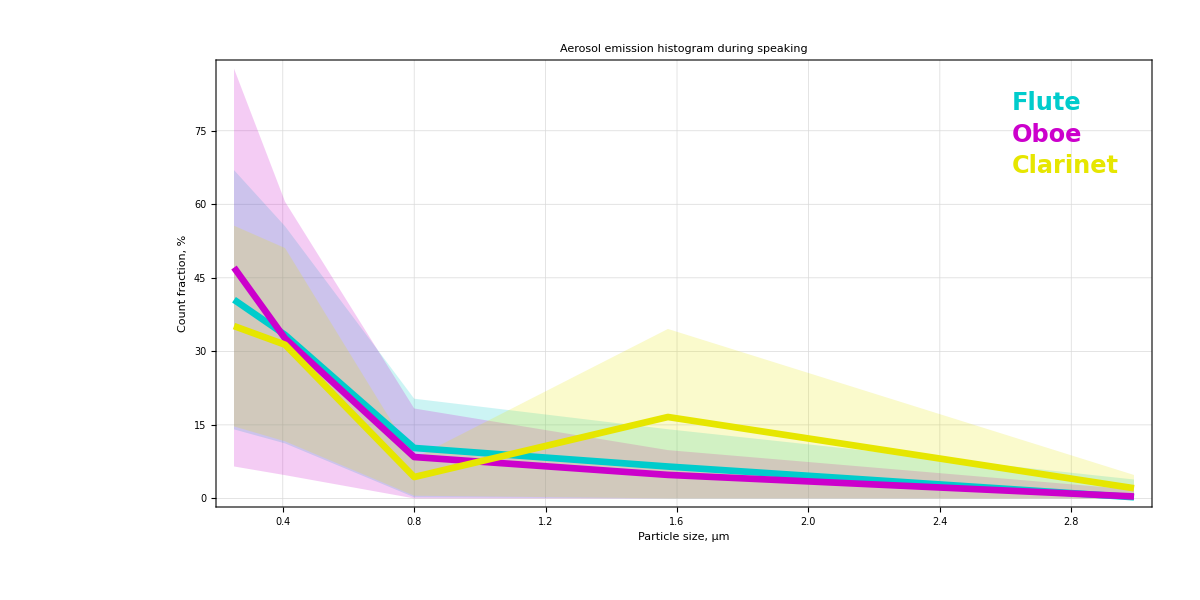

Part::partw: Part 2 of #1 does not exist.

Creating new directory  C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\Fig\Histograms

```mathematica
Clear[b,f,G,H,h,l,M,P,p,Q,q,R,S,s,T,t,v,X]
t = {"Breathing","Playing","Playing With Surgical Mask","Speaking","Speaking With Surgical Mask"}[[

4 (*hier manuell durch die Aufgabennummern durchgehen um die Abb. zu erzeugen. Kann mit Filter KG angewendet werden und ohne*)

]]

X = Select[Y,(#[[4]]===t)&];
X = MyPartition[1,X];
X = Select[X,(Length[#[[2]]]==6)&];
X = Map[{Prepend[Take[#[[2,1]],2],#[[1]]],SortBy[Map[Drop[#,3]&,#[[2]]],First]}&,X];
X = Map[(
h = #[[2,1,2]];
h = PDF[h,x];
h[[1,1,1]] /= NIntegrate[h,Apply[List,#[[2,1,3]][x]][[{2,1,3}]]];
h = ReplacePart[h,#[[2,1,3]][x],{1,1,2}];
ReplacePart[#,Function[x,Evaluate[h]],{2,1}]
)&,X];
Max[Abs[Map[NIntegrate[#[[2,1,2]],{x,0,Infinity}]&,X]-1]]

X = Map[{Append[#[[1]],#[[2,1]]],Rest[#[[2]]]}&,X];
X = Transpose[X];
X[[2]] = Transpose/@Map[{#[[1]],Select[RandomVariate[#[[2]],

100000

],#[[3]]]}&,X[[2]],{2}];
X[[2]] = Transpose[X[[2]]];
b = X[[2,1]];
b = DeleteDuplicates[b];
If[Length[b]==1,
b = First[b]]

X[[2]] = X[[2,2]];
h = Min[Map[Length,X[[2]],{2}]]

X[[2]] = Transpose/@Map[Take[#,h]&,X[[2]],{2}];
X[[2]] = Map[{h=Total[#],#/h}&,X[[2]],{2}];
X = Transpose[X];
X = Transpose[
Map[(
h = #[[1,4]];
{Most[First[#]],
Map[{Round[100*#[[2]]],{h[#[[1]]]}}&,#[[2]]]}
)&,X]];
X[[2]] = Transpose/@Map[(Join@@Outer@@Prepend[#,List])&,X[[2]],{2}];
X[[2]] = Map[
Map[
ReplacePart[#,Total[Flatten[#[[2]]]],2]&,
MyPartition[1,#]]&,
X[[2]],{2}];
X[[2]] = Map[
Transpose[Select[#,(#[[2]]>0)&]]&,
X[[2]],{2}];
X = Transpose[X];
X = Select[X,Not[MemberQ[#[[2]],{}]]&];
Length[X]

X = Transpose[X];
X[[2]] = Map[ReplacePart[#,#[[2]]/Total[#[[2]]],2]&,X[[2]],{2}];
X[[2]] = Map[Transpose[Append[#,Rest[FoldList[Plus,0,#[[2]]]]]]&,X[[2]],{2}];
X[[2]] = Map[{Select[#,(0.05<#[[3]]<=0.95)&],#}&,X[[2]],{2}];
X[[2]] = Map[If[Length[#[[1]]]>2,#[[1]],#[[2]]]&,X[[2]],{2}];
X[[2]] = Map[Most[Transpose[#]]&,X[[2]],{2}];
X[[2]] = Map[(Join@@ConstantArray@@@Transpose[ReplacePart[#,Round[10000*#[[2]]/Total[#[[2]]]],2]])&,X[[2]],{2}];
X = Transpose[X];
X = GatherBy[X,#[[1,2]]&];
X = SortBy[X,(#[[1,1,2]]/.{"Kl"->3,"Qu"->1,"Ob"->2,"Tr"->4,"KP"->5})&];
Map[{#[[1,1,2]],Length[#]}&,X]

p = Map[First,Map[SortBy[#,Last]&,Map[First,X,{2}]],{2}]/.{
"C2"->"C",
"T1"->"T"}
q = Map[StringTake[#,1]&,First/@p]/.{"F"->"Flute","O"->"Oboe","C"->"Clarinet","T"->"Trumpet","S"->"Singing"};
If[t!="Playing",
q = q/.{"Singing"->"Control"}];
q

X = Map[Last,X,{2}];
X = Map[(Join@@@Transpose[#])&,X];
X = Map[Join[#,Flatten[Outer[ConstantArray,MinMax[#],{Round[0.05*Length[#]]}]]]&,X,{2}];

H = Map[Append[Transpose[SortBy[Tally[#],First]],N[1/Length[#]]]&,X,{2}];
H = Map[Transpose[{First[#],Rest[FoldList[Plus,0,Times@@Rest[#]]]}]&,H,{2}];
H = Map[Most,H,{2}];
H = Map[(Rule@@@Transpose[{b,#}])&,H];
H = Rule@@@Transpose[{q,H}];

S = H/.x_:>(
Clear[g,h,i,µ,σ];
g = CDF[NormalDistribution[µ,σ],#]&;
h = Transpose[x];
i = First/@Nearest[Rule@@@Reverse/@x,{0.5,0.8413447460685428,0.15865525393145707}];
i = {First[i],Subtract@@Rest[i]/2};
h = h[[2]]-g/@h[[1]];
h = FindMinimum[h.h,
{{µ,i[[1]]},
{σ,i[[2]]}}];
g = g/.h[[2]];
{g[[1,1]],
Plot[g[z],{z,0,100},
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"%","CDF"},
GridLines->Automatic,
ImageSize->500,
LabelStyle->Prepend[MyTS,FontSize->16],
PlotRange->{All,{0,1}},
Prolog->{Red,PointSize[0.008],Point[x]}]}
)/;If[ListQ[x],If[Depth[x]==3,Dimensions[x][[2]]==2,False],False];
h = 0;
g = Join@@Map[(
++h;
i = #[[1]];
g = 0;
Map[{
{h,2,++g,2,2,2},
StringJoin[i,"    ",RealForm[#[[1]],4,2]," µm"]
}&,#[[2]]]
)&,S];
g = Map[(#[[1]]->Append[Part@@Prepend[#[[1]],S],PlotLabel->#[[2]]])&,g];
S = ReplacePart[S,g];

R = Transpose[List@@@S];
R[[2]] = Map[Prepend[Clip[List@@#[[2,1]],{0,Infinity}],#[[1]]]&,R[[2]],{2}];
T = R[[1]]/.{
"Flute"       ->CMYKColor[1,0,0,0.2],
"Oboe"         ->CMYKColor[0,1,0,0.2],
"Clarinet"->CMYKColor[0,0,1,0.1],
"Trumpet"  ->CMYKColor[0,0.5,1,0],
"Singing"  ->CMYKColor[0,0,0,0.3],
"Control"  ->CMYKColor[0,0,0,0.3]};
T = ColorConvert[T,"HSB"];
P = Map[
Style[#[[1]],
FontColor->#[[2]],
FontFamily->"Arial",
FontSize->(FontSize/.MyTS),
FontWeight->"Bold"]&,
Transpose[{R[[1]],T}]];
M = Map[CountMarker[{#[[1]],#[[2]],#[[3]]^2,True}]&,R[[2]],{2}];
M = ReplaceAll@@@Transpose[{M,Map[(M[[1,1,1]]->#)&,T]}];
T = Map[{Append[#,0.2],#}&,T];
T = Transpose/@Transpose[{T,CredibilityRange/@M}];


s = If[Position[Y,"KP"]=={},0.666,0.55];
s *= (FontSize/.MyTS);

G = BoxWhiskerChart[X,
{{"Whiskers",Thick}},
AspectRatio->0.5,
Axes->False,
ChartLabels->Map[Style[StringJoin[">",RealForm[#,4,2]],s]&,b],
DisplayFunction->Identity,
Frame->True,
FrameLabel->(f={"Particle size,  µm","Count  fraction,  %"}),
GridLines  ->Automatic,
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->(l=StringJoin["Aerosol emission histogram during ",ToLowerCase[t]]),
PlotRange->{All,{0,100}},
Prolog->{
GrayLevel[0],Map[
Text[
Style[#[[1]],FontSize->1.25*s,FontWeight->"Bold"],
Scaled[{#[[2]],v=0.985}],{0,1}]&,
Transpose[{q,
h = Switch[Length[q],
1,0.5,
2,0.275,
3,0.2,
4,0.163,
5,0.14];
h = EquallySpaced[h,1-h,Length[q]]}]],
GrayLevel[0.5],Map[
Text[
Style[#[[1]],FontSize->0.87*s,FontWeight->"Plain"],
Scaled[{#[[2]],v-0.05}],{0,1}]&,
Transpose[{Map[ConcatStringList[#," "]&,p],h}]]}]


Q = Graphics[
{Thickness[0.004],Transpose[T]},
AspectRatio->0.5,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->f,
GridLines  ->Automatic,
ImageSize->1200,
LabelStyle->MyTS,
PlotLabel->l,
PlotRange->{All,{0,All}},
PlotRangeClipping->True,
Prolog->(h=1;Map[Text[#,Scaled[{0.85,h-=0.07}],{-1,1}]&,P])]


G = Rasterize[G,RasterSize->3000];
Q = Rasterize[Q,RasterSize->2000];

If[ImageQ[G],
Column[{
ImageType[G],
ImageChannels[G],
ImageDimensions[G],
SaveAsTIF[f=
StringJoin[DatenOrdner,"Fig\\Histograms\\",l,
If[Position[Y,"KP"]=={},""," incl KP"],
".tif"],i=
{"BoxWhiskerChart"->G,
"SpectraGraphics"->Q,
"CDF"->H,
"MeanEstimates"->S,
"SpectraData"->Rule@@@Transpose[R],
"Markers"->Rule@@@Transpose[{R[[1]],M}],
"CredibilityRanges"->Rule@@@Transpose[{R[[1]],T}]}]
}]]

Select[
Transpose[{LoadFromTIF[False,f],i}],
Not[TrueQ[SameQ@@#]]&];
Max[Abs[ImageData/@ImageDifference@@@Map[Last,%,{2}]]]==0
```

#### output is online https://github.com/Carl-Firle/my-data-storage/tree/main/data/20220301-01/Fig/Histograms

```mathematica
(*Ende*)
```